## Verify and Plot

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
myPlot2D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];
(*plot init and unsafe regions*)
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.4], Green},BoundaryStyle->None ,PlotPoints-> 100];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Red},BoundaryStyle->None,PlotPoints-> 100];

(*plot sample trajectories*)
sampleNum = 20;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];(*NDSolve[{varSet[[1]]'[t]==ReplaceAll[flowVec[[1]],{varSet[[1]]-> varSet[[1]][t],varSet[[2]]-> varSet[[2]][t]}],
varSet[[2]]'[t]==ReplaceAll[flowVec[[2]],{varSet[[1]]-> varSet[[1]][t],varSet[[2]]-> varSet[[2]][t]}],
varSet[[1]][0] == s0[[1]],varSet[[2]][0]==s0[[2]]},varSet,{t,20}];*)
trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
(*
trajPlot[s0_]:= ParametricPlot[Evaluate[{varSet[[1]][t],varSet[[2]][t]}/. (solution[s0])],{t,0,20},PlotStyle->{Black}];
trajPlotAll =Table[trajPlot[initSamples[[i]]],{i,sampleNum}];
*)
bcPlot=RegionPlot[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.2],Green},BoundaryStyle-> {Green},PlotPoints-> 100];
bchPlot=RegionPlot[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.1],Blue},BoundaryStyle->{Blue},PlotPoints-> 100];
Print[Show[flowPlot,initPlot,unsafePlot,trajPlot,bcPlot,bchPlot, FrameLabel->varSet]]
]

myPlot3D [varSet_,varRange_,flowVec_,unsafeBoundary_,initBoundary_,bc_,bch_]:= Module[
{ranges,flowPlot,initCons,unsafeCons,initPlot,unsafePlot,initSamples,flow,trajGen,trajTable,trajPlot,sampleNum,solution,trajPlotAll,bcPlot,bchPlot},
Print["Plot3d..."];
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];
(*flowPlot =VectorPlot3D[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->{Opacity[0.4],Gray}];*)
(*plot init and unsafe regions*)
initCons=And@@Thread[GreaterEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[GreaterEqualThan[0][unsafeBoundary]];
initPlot=RegionPlot3D[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.4], Green},BoundaryStyle->None ,PlotPoints-> 100];
unsafePlot=RegionPlot3D[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Red},BoundaryStyle->None,PlotPoints-> 100];
(*plot sample trajectories*)

sampleNum = 1;
initSamples=RandomPoint[ImplicitRegion[initCons&&varRange[[1]][[1]]≤ varSet[[1]]≤ varRange[[1]][[2]]&& varRange[[2]][[1]]≤ varSet[[2]]≤ varRange[[2]][[2]]&&varRange[[3]][[1]]≤ varSet[[3]]≤ varRange[[3]][[2]],varSet],sampleNum];
Off[NDSolve::ndsz];
solution[s0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==s0]],varSet,{t,0,20},Method->"StiffnessSwitching"];(*NDSolve[{varSet[[1]]'[t]==ReplaceAll[flowVec[[1]],{varSet[[1]]-> varSet[[1]][t],varSet[[2]]-> varSet[[2]][t]}],
varSet[[2]]'[t]==ReplaceAll[flowVec[[2]],{varSet[[1]]-> varSet[[1]][t],varSet[[2]]-> varSet[[2]][t]}],
varSet[[1]][0] == s0[[1]],varSet[[2]][0]==s0[[2]]},varSet,{t,20}];*)
trajPlot=ParametricPlot3D[Evaluate[(#[t]&/@varSet)/.solution[#]&/@initSamples],{t,0,20},PlotStyle->Directive[Black,Thickness[Large]]];
(*
trajPlot[s0_]:= ParametricPlot[Evaluate[{varSet[[1]][t],varSet[[2]][t]}/. (solution[s0])],{t,0,20},PlotStyle->{Black}];
trajPlotAll =Table[trajPlot[initSamples[[i]]],{i,sampleNum}];
*)
bcPlot=RegionPlot3D[bc≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.2],Green},BoundaryStyle-> {Green},PlotPoints-> 100];
bchPlot=RegionPlot3D[bch≤ 0,Evaluate[ranges],PlotStyle->{Opacity[0.1],Blue},BoundaryStyle->{Blue},PlotPoints-> 100];
Print[Show[initPlot,unsafePlot,trajPlot,bcPlot,bchPlot, FrameLabel->varSet]]
];

myVerify [varSet_,flowVec_,initBoundary_,unsafeBoundary_,bc_,deg_]:= Module[
{lambda,unsafeCons,initCons,bcLie,bc1,bc2,bc3,bc4,timev},
timev=Now;
lambda = -1;
unsafeCons = And@@(GreaterEqual[#,0]&/@unsafeBoundary);
initCons = And@@(GreaterEqual[#,0]&/@initBoundary);
bcLie =D[bc,varSet[[1]]]*flowVec[[1]]+D[bc,varSet[[2]]]*flowVec[[2]];

bc1 = FindInstance[bc>0&&initCons,varSet];
bc2 =FindInstance[bc≤ 0&&unsafeCons,varSet];
bc3 =FindInstance[bcLie-lambda*bc> 0,varSet];
bc4 =FindInstance[bc== 0&&bcLie> 0,varSet];
Print["deg: ",deg, "  ",bc1,bc2,bc3,bc4];
If[Or[Length[bc1]+Length[bc2]+Length[bc3]==0,Length[bc1]+Length[bc2]+Length[bc4]==0],
Return[1],
Return[0]];
]

verifyResults[benchmark_,plot_,plotRange_]:= Module[
{systemPath,varSet,flowVec,initCons,unsafeCons,bcPath,bcData,ebc,hbc,ebcDeg,hbcDeg,totaltime,totalsdptime,time,etime,htime,ptime,result,i,degmax},
systemPath=FileNameJoin[{".","Results","systems",StringJoin[benchmark,".txt"]}];
{varSet,flowVec,initCons,unsafeCons} = ReadList[systemPath];
ebcDeg=0;
hbcDeg=0;
Print["Variables: ",varSet];
Print["Flow: ",flowVec];
Print["Initial: ",initCons];
Print["Unsafe: ",unsafeCons];
degmax=6;

Print["Verifying SUFFICIENT condition results..."];
bcPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ degmax,i++,
ebc = bcData[[i]][[1]];
time = bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,ebc,i],10,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + result[[1]];
If[result[[2]]== 1,
ebcDeg=i;
Print["Verified at degree ",ebcDeg];
Print[ebc];
Break[]
];
If[result[[2]]== 2,
ebcDeg=i;
Print["Verify out of time at degree ",ebcDeg];
Print[ebc];
Break[]
];
];
etime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[ebcDeg>0,
Print["sufficient condition: verified at degree ", ebcDeg, "  time used: ",etime];,
Print["No valid soltion, time used: ",etime];
];

Print["Verifying Necessary results..."];
bcPath=FileNameJoin[{".","Results","necessary",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
totaltime=0;
totalsdptime=0;
For[i= 1,i≤ degmax,i++,
hbc = bcData[[i]][[1]];
time =bcData[[i]][[2]];
result=Timing[TimeConstrained[myVerify[varSet, flowVec,initCons, unsafeCons,hbc,i],10,2]];
totaltime = totaltime+time+result[[1]];
totalsdptime = totalsdptime + result[[1]];
If[result[[2]]== 1,
hbcDeg=i;
Print["Verified at degree ",hbcDeg];
Print[hbc];
Break[]
];
If[result[[2]]== 2,
hbcDeg=i;
Print["Verify out of time at degree ",hbcDeg];
Print[hbc];
Break[]
];
];
htime =totaltime;
Print["totalsdptime: ",totalsdptime ];
If[hbcDeg>0,
Print["Necessary condition: verified at degree ", hbcDeg, "  time used: ",htime];,
Print["No valid soltion, time used: ",htime];
];
If[ plot== 1,
If[Length[varSet]== 2,myPlot2D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc]]];
If[Length[varSet]== 3,myPlot3D[varSet,plotRange,flowVec,unsafeCons,initCons,If[ebcDeg== 0,1,ebc],If[hbcDeg== 0,1,hbc]]];
]
]
tryResults[benchmark_,plot_,plotRange_,bcDeg_,hDeg_]:= Module[
{systemPath,varSet,flowVec,initCons,unsafeCons,bcPath,bcData,ebc,hbc,ebcDeg,hbcDeg,totaltime,time,etime,htime,ptime,result,i,degmax},
systemPath=FileNameJoin[{".","Results","systems",StringJoin[benchmark,".txt"]}];
{varSet,flowVec,initCons,unsafeCons} = ReadList[systemPath];
ebcDeg=0;
hbcDeg=0;
degmax=8;
Print["Variables: ",varSet];
Print["Flow: ",flowVec];
Print["Initial: ",initCons];
Print["Unsafe: ",unsafeCons];

bcPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
If[bcDeg== 0,ebc=1,ebc = bcData[[bcDeg]][[1]]];

bcPath=FileNameJoin[{".","Results","homogenization",StringJoin[benchmark,".txt"]}];
bcData=ReadList[bcPath,{Expression,Expression},RecordSeparators-> "\n"];
If[hDeg== 0,hbc= 1,hbc = bcData[[hDeg]][[1]]];

myPlot3D[varSet,plotRange,flowVec,unsafeCons,initCons,ebc,hbc]
]
```

## Benchmarks

Variables: {x1,x2}

Flow: {x2,-x1+0.333333 x1^3-x2}

Initial: {-2.+3. x1-x1^2-x2^2}

Unsafe: {-1.84-2. x1-x1^2-2. x2-x2^2}

Verifying SUFFICIENT condition results...

deg: 1  {}{{x1→-1.,x2→-1.4}}{}{}

deg: 2  {}{}{}{}

Verified at degree 2

-1.77111-1.60813 x1-0.417577 x1^2-2.30397 x2-1.11342 x1 x2

totalsdptime: 0.97483

sufficient condition: verified at degree 2  time used: 1.2735

Verifying Necessary results...

deg: 1  {}{}{{x1→-1.×10^8,x2→1.×10^8}}{{x1→-1.×10^8,x2→9.53415×10^7}}

deg: 2  {}{}{}{}

Verified at degree 2

-4.31556-4.1499 x1-1.11382 x1^2-5.48978 x2-2.93671 x1 x2-0.0000494508 x2^2

totalsdptime: 1.06583

Necessary condition: verified at degree 2  time used: 1.32115

Plot2d...

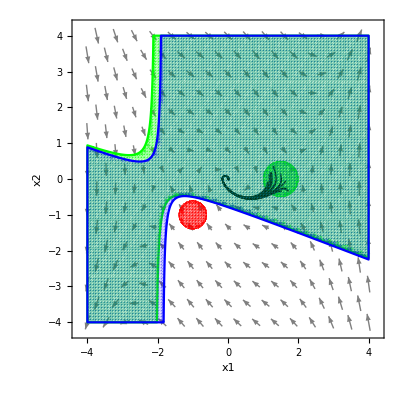

```mathematica
benchmarkname = "barrier-1";
plotRange = {{-4,4},{-4,4}}; 
verifyResults[benchmarkname,1,plotRange]
```

```mathematica
benchmarkname = "lorenz";
plotRange = {{-4,4},{-4,4}};
plotRange = {{-20,20},{-20,20}}; 
verifyResults[benchmarkname,1,plotRange]
```

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-576.5-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-488.5-33. x1-x1^2-29. x2-x2^2+5. x3-x3^2}

Verifying SUFFICIENT condition results...

deg: 1  {}{{x1→-16.5,x2→-14.5,x3→3.}}{}{}

Divide::infy: Infinite expression 1/(0``-12.790288697650146) encountered.

Infinity::indet: Indeterminate expression 0``-14.342107508088962 ComplexInfinity encountered.

deg: 2  {}{{x1→-16.5,x2→-14.5,x3→2.25}}{{x1→-17.6957,x2→19.1745,x3→66.468}}{{x1→-2.17896,x2→0.,x3→-11.556}}

deg: 3  {}{{x1→-16.5,x2→-14.5,x3→2.25}}{{x1→1.,x2→-1.,x3→1.88371×10^6}}{{x1→-7.19494,x2→-10.7924,x3→-10.0729}}

Verify out of time at degree 4

-14.8316-0.0817262 x1+0.110719 x1^2-0.000709241 x1^3+0.000198846 x1^4-0.0792919 x2-0.0311069 x1 x2+0.000178263 x1^2 x2+0.0556832 x2^2-0.000059001 x1 x2^2-0.0000400039 x1^2 x2^2-0.000458407 x2^3+0.0000634791 x2^4-4.06035 x3+0.025107 x1 x3-0.00236781 x1^2 x3+0.0246691 x2 x3+0.000361532 x1 x2 x3-0.00651313 x2^2 x3+0.230538 x3^2-0.000443465 x1 x3^2-0.0000400039 x1^2 x3^2-0.000473356 x2 x3^2+0.000126958 x2^2 x3^2-0.00620346 x3^3+0.0000634791 x3^4

totalsdptime: 14.1491

sufficient condition: verified at degree 4  time used: 14.7398

Verifying HOMOGENIZATION results...

deg: 1  {}{{x1→-16.5,x2→-14.5,x3→3.}}{}{}

deg: 2  {}{{x1→-17.,x2→-14.5,x3→2.5}}{{x1→-1.,x2→-107.987,x3→0.}}{{x1→0.,x2→1103.75,x3→-224.883}}

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0``-0.8016560058719694 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

deg: 3  {}{{x1→-16.5,x2→-14.5,x3→2.25}}{{x1→200.432,x2→-1562.62,x3→-1.}}{{x1→95.1429,x2→216,x3→471/5}}

Verify out of time at degree 4

-4.5304×10^7-489168. x1+135247. x1^2+1731.62 x1^3+438.651 x1^4-339617. x2-77619.3 x1 x2+305.465 x1^2 x2+8.34252 x1^3 x2+224646. x2^2-2198.72 x1 x2^2-99.1754 x1^2 x2^2-1952.21 x2^3+8.19394 x1 x2^3+232.56 x2^4-1.41589×10^7 x3+168144. x1 x3-480.079 x1^2 x3-0.390109 x1^3 x3+122039. x2 x3-931.857 x1 x2 x3+3.07919 x1^2 x2 x3-24555.9 x2^2 x3+0.415957 x1 x2^2 x3+3.45245 x2^3 x3+884185. x3^2-3862.97 x1 x3^2-99.5112 x1^2 x3^2-2179.95 x2 x3^2+9.57953 x1 x2 x3^2+464.372 x2^2 x3^2-24119.3 x3^3+0.567198 x1 x3^3+3.70339 x2 x3^3+231.572 x3^4

totalsdptime: 14.8616

sufficient condition: verified at degree 4  time used: 16.3913

Plot3d...

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Prepend,{{{-20,20},{-20,20}},{x1,x2,x3}}]; dimensions are 2 and 3.

RegionPlot3D::argrx: RegionPlot3D called with 3 arguments; 4 arguments are expected.

ImplicitRegion::msgs: Evaluation of {initCons$509559&&{{-20,20},{-20,20}}⟦1⟧⟦1⟧≤{x1,x2,x3}⟦1⟧≤{{-20,20},{-20,20}}⟦1⟧⟦2⟧&&{{-20,20},{-20,20}}⟦2⟧⟦1⟧≤{x1,x2,x3}⟦2⟧≤{{-20,20},{-20,20}}⟦2⟧⟦2⟧&&{{-20,20},{-20,20}}⟦3⟧⟦1⟧≤{x1,x2,x3}⟦3⟧≤{{-20,20},{-20,20}}⟦3⟧⟦2⟧,True} generated message(s) {Part::partw}.

RandomPoint::creg: The first argument ImplicitRegion[-576.5-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2≥0&&-20≤x1≤20&&-20≤x2≤20&&{{-20,20},{-20,20}}≤x3≤3,{x1,x2,x3}] is expected to be a parameter-free region.

NDSolve::dvnoarg: The function x1 appears with no arguments.

ReplaceAll::reps: {NDSolve[{x1'[t]==-10. x1[t]+10. x2[t],x2'[t]==28. x1[t]-x2[t]-x1[t] x3[t],x3'[t]==x1[t] x2[t]-2.66667 x3[t],x1[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}],x2[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}],x3[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}]},{x1,x2,x3},{t,0,20},Method→StiffnessSwitching]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomPoint::creg: The first argument {x1[t],x2[t],x3[t]}/.NDSolve[{x1'[t]==-10. x1[t]+10. x2[t],x2'[t]==28. x1[t]-x2[t]-x1[t] x3[t],x3'[t]==x1[t] x2[t]-2.66667 x3[t],x1[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}],x2[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}],x3[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}]},{x1,x2,x3},{t,0,20},Method→StiffnessSwitching] is expected to be a parameter-free region.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x1'[0.000408571]==-10. x1[0.000408571]+10. x2[0.000408571],x2'[0.000408571]==28. x1[0.000408571]-x2[0.000408571]-x1[0.000408571] x3[0.000408571],x3'[0.000408571]==x1[0.000408571] x2[0.000408571]-2.66667 x3[0.000408571],x1[0]==«1»,x2[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}],x3[0]==ImplicitRegion[Plus[«7»]≥0&&-20≤x1≤20&&-20≤x2≤20&&{«2»}≤x3≤3,{x1,x2,x3}]},«1»,«1»,«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomPoint::creg: The first argument {x1[0.000408571],x2[0.000408571],x3[0.000408571]}/.NDSolve[«1»] is expected to be a parameter-free region.

General::stop: Further output of RandomPoint::creg will be suppressed during this calculation.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x1'[0.000408571]==-10. x1[0.000408571]+10. x2[0.000408571],x2'[0.000408571]==28. x1[0.000408571]-1. x2[0.000408571]-1. x1[0.000408571] x3[0.000408571],x3'[0.000408571]==x1[0.000408571] x2[0.000408571]-«19» x3[«22»],x1[0.]==«1»,x2[0.]==ImplicitRegion[Plus[«7»]≥0.&&-20.≤x1≤20.&&-20.≤x2≤20.&&{«2»}≤x3≤3.,{x1,x2,x3}],x3[0.]==ImplicitRegion[Plus[«7»]≥0.&&-20.≤x1≤20.&&-20.≤x2≤20.&&{«2»}≤x3≤3.,{x1,x2,x3}]},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408572 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

RegionPlot3D::argrx: RegionPlot3D called with 3 arguments; 4 arguments are expected.

General::stop: Further output of RegionPlot3D::argrx will be suppressed during this calculation.

Show::gtype: RegionPlot3D is not a type of graphics.

```mathematica
benchmarkname = "lorenz";
plotRange = {{-20,20},{-20,20},{-20,20}}; 
tryResults[benchmarkname,1,plotRange,0,0]
```

Variables: {x1,x2,x3}

Flow: {-10. x1+10. x2,28. x1-x2-x1 x3,x1 x2-2.66667 x3}

Initial: {-572.75-29. x1-x1^2-29. x2-x2^2+25. x3-x3^2}

Unsafe: {-484.75-33. x1-x1^2-29. x2-x2^2+5. x3-x3^2}

Plot3d...

-Graphics3D-